## F4 definition from ArXiv : 0905.0097

We collect the Analytic continuations from the file F4_derivation.nb

```mathematica
f4num[a_,b_,c_,d_,x_,y_]:=(Pochhammer[a,m+n]Pochhammer[b,m+n] x^m y^n)/(Pochhammer[c,m]Pochhammer[d,n]m!n!)
```

```mathematica
F4AC1[a_,b_,c_,d_,x_,y_,m_,n_] = (Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!)
```

(x^m y^n Pochhammer[a,m+n] Pochhammer[b,m+n])/(m! n! Pochhammer[c,m] Pochhammer[d,n])

```mathematica
F4roc1[x_,y_]=√Abs[x]+√Abs[y]<1
```

√Abs[x]+√Abs[y]<1

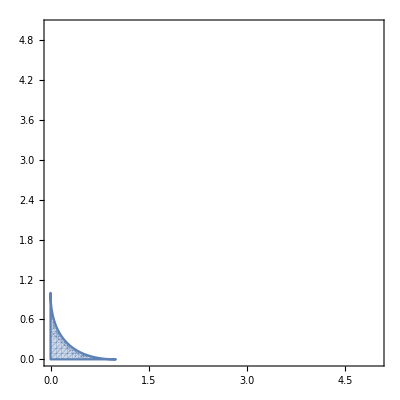

```mathematica
RegionPlot[{F4roc1[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC2[a_,b_,c_,d_,x_,y_,m_,n_] = ((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+((1-x)^(-a-b+c+m-2 n) y^n Gamma[a+b-c] Gamma[c] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n] Pochhammer[-a+c,m-n] Pochhammer[-b+c,m-n])/(m! n! Gamma[a] Gamma[b] Pochhammer[1-a-b+c,m-2 n] Pochhammer[d,n]);
```

```mathematica
F4roc2[x_,y_]=√Abs[1-x]<1&&√Abs[y]<2&&(1+√(1-Abs[1-x])>√Abs[y]||√(1-Abs[1-x])+√Abs[y]<1)&&Abs[1-x]<1&&√Abs[y/(-1+x)^2]<-1/Abs[1-x]+(√(1+Abs[1-x]))/Abs[1-x]&&4 Abs[y/(-1+x)^2]<1;
```

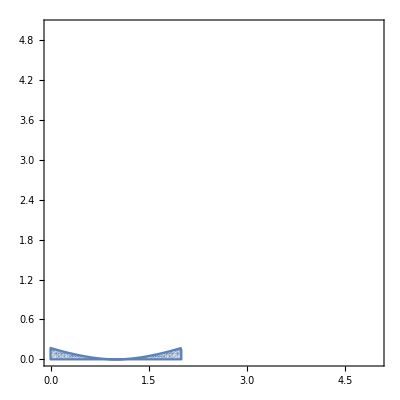

```mathematica
RegionPlot[{F4roc2[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC3[a_,b_,c_,d_,x_,y_,m_,n_]:= F4AC2[a,b,d,c,y,x,n,m]
```

```mathematica
F4roc3[x_,y_]:=F4roc2[y,x]
```

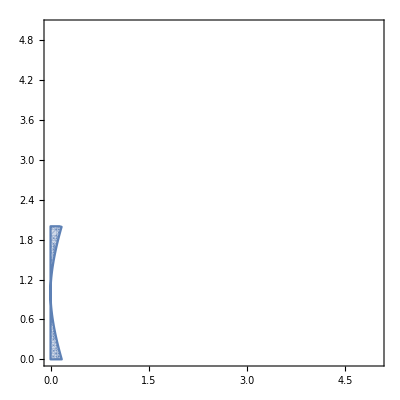

```mathematica
RegionPlot[{F4roc3[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC4[a_,b_,c_,d_,x_,y_,m_,n_] =((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+
(2^(-2 n) √π (2-2 x)^(-a-b+c+m) ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2-a/2-b/2+c/2+m/2) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(y m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2])-(2^(1-2 n) √π (2-2 x)^(-a-b+c+m) x ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2-a/2-b/2+c/2+m/2) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(y m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2])+(2^(-2 n) √π (2-2 x)^(-a-b+c+m) x^2 ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2-a/2-b/2+c/2+m/2) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(y m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2])+(2^(-2 n) √π (2-2 x)^(-a-b+c+m) ((-1+x)^2/y)^n (-y/(-1+x)^2)^(-a/2-b/2+c/2+m/2) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (2+a-b-c),m/2] Pochhammer[1/2 (2-a+b-c),m/2] Pochhammer[1/2 (a+b-c),-m/2+n] Pochhammer[1/2 (a-b+c),-m/2] Pochhammer[1/2 (a-b+c),m/2+n] Pochhammer[1/2 (-a+b+c),-m/2] Pochhammer[1/2 (-a+b+c),m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-c)] Gamma[1/2 (-a-b+c+2 d)] Pochhammer[1/2,n] Pochhammer[1/2 (2+a-b-c),-m/2] Pochhammer[1/2 (2-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (a-b+c),m/2] Pochhammer[1/2 (a-b+c),-m/2+n] Pochhammer[1/2 (-a+b+c),m/2] Pochhammer[1/2 (-a+b+c),-m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2] Pochhammer[1/2 (-a-b+c+2 d),m/2]);
```

```mathematica
F4roc4[x_,y_]=Abs[(-1+x) √(-y/(-1+x)^2)]<2&&√Abs[(-1+x)^2/y]+Abs[(-1+x) √(-y/(-1+x)^2)]<2&&Abs[(-1+x)^2/y]<4;
```

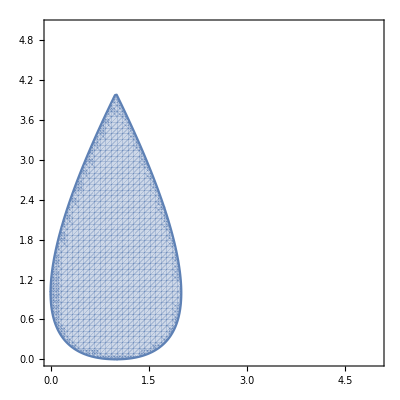

```mathematica
RegionPlot[{F4roc4[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC5[a_,b_,c_,d_,x_,y_,m_,n_]:=F4AC4[a,b,d,c,y,x,n,m]
```

```mathematica
F4roc5[x_,y_]:=F4roc4[y,x]
```

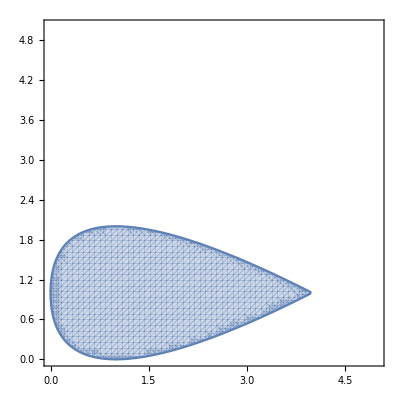

```mathematica
RegionPlot[{F4roc5[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC6[a_,b_,c_,d_,x_,y_,m_,n_] = ((-1)^n (-x)^(-a-n) x^-m y^n Gamma[-a+b] Gamma[c] Pochhammer[a,m+n] Pochhammer[1+a-c,m+n])/(m! n! Gamma[b] Gamma[-a+c] Pochhammer[1+a-b,m] Pochhammer[d,n])+((-1)^n (-x)^(-b-n) x^-m y^n Gamma[a-b] Gamma[c] Pochhammer[b,m+n] Pochhammer[1+b-c,m+n])/(m! n! Gamma[a] Gamma[-b+c] Pochhammer[1-a+b,m] Pochhammer[d,n]);
```

```mathematica
F4roc6[x_,y_]=Abs[x]>1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1;
```

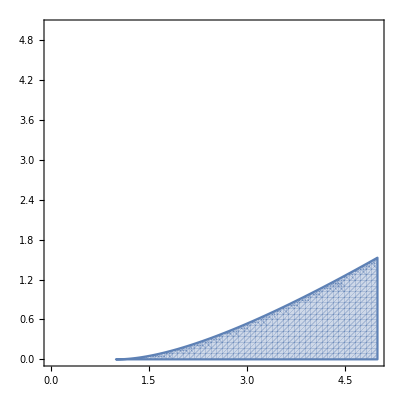

```mathematica
RegionPlot[{F4roc6[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

```mathematica
F4AC7[a_,b_,c_,d_,x_,y_,m_,n_]:=F4AC6[a,b,d,c,y,x,n,m]
```

```mathematica
F4roc7[x_,y_]:=F4roc6[y,x]
```

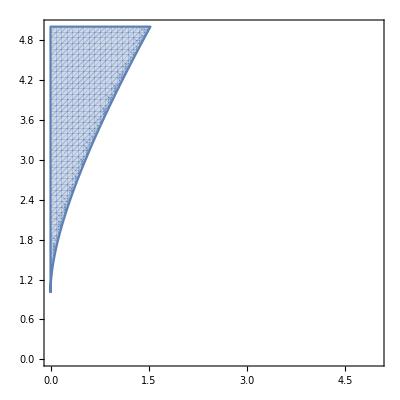

```mathematica
RegionPlot[{F4roc7[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

## KdF definition from ArXiv : 0905.0097

We collect the Analytic continuations from the file KdF_derivation.nb

```mathematica
KdF[{alpha_List,beta_List,gamma_List},{alpha1_List,beta1_List,gamma1_List},{x_,y_}]:=(Times@@Pochhammer[alpha,m+n]Times@@Pochhammer[beta,m]Times@@Pochhammer[gamma,n] x^m y^n)/(Times@@Pochhammer[alpha1,m+n]Times@@Pochhammer[beta1,m]Times@@Pochhammer[gamma1,n]m!n!)
```

```mathematica
KdF[{{a1,a2},{b1},{}},{{},{c1,c2},{d1}},{x,y}]
```

(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n])

```mathematica
Abs[x]<1&&√Abs[x]+√Abs[y]<1&&Abs[y]<1
```

Abs[x]<1&&√Abs[x]+√Abs[y]<1&&Abs[y]<1

```mathematica
KdFAC1[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m y^n Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m])/(m! n! Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[d1,n]);
```

```mathematica
KdFROC1[x_,y_]=Abs[x]<1&&√Abs[x]+√Abs[y]<1&&Abs[y]<1;
```

```mathematica
RegionPlot[{KdFROC1[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

-Graphics-

Around (inf,0) by inverting 3F2(...x) - Equation C-12 in the paper

Notice that the following result should match with Eq. C-12 in the paper but their result and our result differ via exchange of e <-> f

```mathematica
KdFFAC2[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b1] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b1] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b1,m+n] Pochhammer[d1,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b1] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b1] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b1,m+n] Pochhammer[d1,n])+((-x)^-b1 x^-m y^n Gamma[a1-b1] Gamma[a2-b1] Gamma[c1] Gamma[c2] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Pochhammer[1-a1+b1,m-n] Pochhammer[1-a2+b1,m-n] Pochhammer[d1,n]);
```

```mathematica
KdFROC2[x_,y_]=Abs[x]<x^2&&1+√Abs[y]<√Abs[x]&&Abs[y]<1&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1;
```

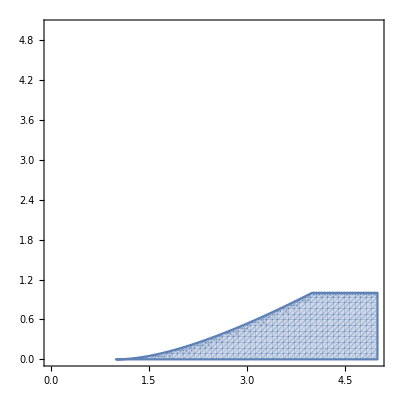

```mathematica
RegionPlot[{KdFROC2[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

(inf,inf) AC obtained by inverting one series of KdFAC1.

```mathematica
KdFFAC3[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^m (-x)^-b1 x^-m (-y)^(-a1+b1+m) y^-n Gamma[-a1+a2] Gamma[a1-b1] Gamma[c1] Gamma[c2] Gamma[d1] Pochhammer[a1-b1,-m+n] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1+a1-b1-d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Gamma[-a1+b1+d1] Pochhammer[1+a1-a2,n])+((-1)^m (-x)^-b1 x^-m (-y)^(-a2+b1+m) y^-n Gamma[a1-a2] Gamma[a2-b1] Gamma[c1] Gamma[c2] Gamma[d1] Pochhammer[a2-b1,-m+n] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1+a2-b1-d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Gamma[-b1+c1] Gamma[-b1+c2] Gamma[-a2+b1+d1] Pochhammer[1-a1+a2,n])+((-1)^n (-x)^(-a1-n) x^-m y^n Gamma[-a1+a2] Gamma[-a1+b1] Gamma[c1] Gamma[c2] Pochhammer[a1,m+n] Pochhammer[1+a1-c1,m+n] Pochhammer[1+a1-c2,m+n])/(m! n! Gamma[a2] Gamma[b1] Gamma[-a1+c1] Gamma[-a1+c2] Pochhammer[1+a1-a2,m] Pochhammer[1+a1-b1,m+n] Pochhammer[d1,n])+((-1)^n (-x)^(-a2-n) x^-m y^n Gamma[a1-a2] Gamma[-a2+b1] Gamma[c1] Gamma[c2] Pochhammer[a2,m+n] Pochhammer[1+a2-c1,m+n] Pochhammer[1+a2-c2,m+n])/(m! n! Gamma[a1] Gamma[b1] Gamma[-a2+c1] Gamma[-a2+c2] Pochhammer[1-a1+a2,m] Pochhammer[1+a2-b1,m+n] Pochhammer[d1,n]);
```

```mathematica
KdFROC3[x_,y_]=1/Abs[x]<1&&1/Abs[y]<1&&1+1/(√Abs[y])<1/(√Abs[y/x])&&1/(√Abs[x])+√Abs[y/x]<1&&Abs[y/x]<1;
```

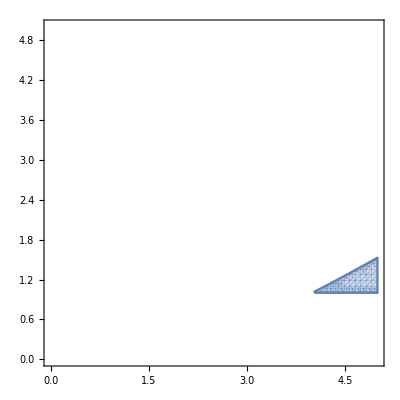

```mathematica
RegionPlot[{KdFROC3[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

(0,1) AC

```mathematica
KdFFAC4[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(x^m (1-y)^(-a1-a2+d1-2 m+n) Gamma[a1+a2-d1] Gamma[d1] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m] Pochhammer[-a1+d1,-m+n] Pochhammer[-a2+d1,-m+n])/(m! n! Gamma[a1] Gamma[a2] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1-a1-a2+d1,-2 m+n]);
```

```mathematica
KdFROC4[x_,y_]=√Abs[1-y]<1&&((√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y]&&√Abs[x]<1)||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2))&&Abs[x/(-1+y)^2]<1/4&&√Abs[1-y]<(√(1-2 √Abs[x/(-1+y)^2]))/(√Abs[x/(-1+y)^2])&&Abs[1-y]<1;
```

```mathematica
RegionPlot[{KdFROC4[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

-Graphics-

(inf,inf) AC by inverting 2F1(y) of KdFAC1

```mathematica
KdFAC5[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=((-1)^m x^m (-y)^(-a1-m) y^-n Gamma[-a1+a2] Gamma[d1] Pochhammer[a1,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m+n])/(m! n! Gamma[a2] Gamma[-a1+d1] Pochhammer[1+a1-a2,n] Pochhammer[c1,m] Pochhammer[c2,m])+((-1)^m x^m (-y)^(-a2-m) y^-n Gamma[a1-a2] Gamma[d1] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a2-d1,m+n])/(m! n! Gamma[a1] Gamma[-a2+d1] Pochhammer[1-a1+a2,n] Pochhammer[c1,m] Pochhammer[c2,m]);
```

```mathematica
KdFFAC5[a,b,c,d,e,f,x,y,m,n]
```

KdFFAC5[a,b,c,d,e,f,x,y,m,n]

```mathematica
KdFROC5[x_,y_]=Abs[x/y]<1&&√Abs[x/y]+1/(√Abs[y])<1&&Abs[y]>1;
```

```mathematica
RegionPlot[{KdFROC5[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

-Graphics-

Another AC around (0,1)

```mathematica
KdFAC6us[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=(x^m (1-y)^n Gamma[d1] Gamma[-a1-a2+d1] Pochhammer[a1,m+n] Pochhammer[a2,m+n] Pochhammer[b1,m] Pochhammer[1+a1-d1,m] Pochhammer[1+a2-d1,m])/(m! n! Gamma[-a1+d1] Gamma[-a2+d1] Pochhammer[c1,m] Pochhammer[c2,m] Pochhammer[1+a1+a2-d1,2 m+n])+(4^-m (1-y)^(-a1-a2+d1+n) ((-1+y)^2/x)^m Gamma[c1] Gamma[c2] Gamma[a1+a2-d1] Gamma[d1] ((4^-b1 (-x/(-1+y)^2)^-b1 Gamma[1/2 (a1+a2-2 b1-d1)] Gamma[1/2 (1+a1+a2-2 b1-d1)] Pochhammer[b1,m] Pochhammer[1+b1-c1,m] Pochhammer[1+b1-c2,m] Pochhammer[1/2 (a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (1+a1+a2-2 b1-d1),-n/2] Pochhammer[-a1+b1+d1,m+n] Pochhammer[-a2+b1+d1,m+n] Pochhammer[1/2 (1-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),n/2])/(Gamma[-b1+c1] Gamma[-b1+c2] Pochhammer[-a1+b1+d1,m] Pochhammer[-a2+b1+d1,m] Pochhammer[1/2 (1-a1-a2+2 b1+d1),m+n/2] Pochhammer[1/2 (2-a1-a2+2 b1+d1),m+n/2])+(2^(-a1-a2+d1+n) √π (-x/(-1+y)^2)^(1/2 (-1-a1-a2+d1+n)) (√(-x/(-1+y)^2) Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (-a1-a2+2 b1+d1)] Gamma[1/2 (-1-a1-a2+2 c1+d1)] Gamma[1/2 (-1-a1-a2+2 c2+d1)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a1-a2-d1),-n/2] Pochhammer[1/2 (2+a1-a2-d1),n/2] Pochhammer[1/2 (1-a1+a2-d1),-n/2] Pochhammer[1/2 (2-a1+a2-d1),n/2] Pochhammer[1/2 (a1+a2-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),-n/2] Pochhammer[1/2 (a1-a2+d1),m+n/2] Pochhammer[1/2 (a1-a2+d1),-n/2] Pochhammer[1/2 (1+a1-a2+d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),n/2] Pochhammer[1/2 (-a1+a2+d1),m+n/2] Pochhammer[1/2 (-a1+a2+d1),-n/2] Pochhammer[1/2 (1-a1+a2+d1),m-n/2] Pochhammer[1/2 (1-a1+a2+d1),n/2] Pochhammer[1/2 (-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c2+d1),n/2]-Gamma[1/2 (1+a1+a2-d1)] Gamma[1/2 (-1-a1-a2+2 b1+d1)] Gamma[1/2 (-a1-a2+2 c1+d1)] Gamma[1/2 (-a1-a2+2 c2+d1)] Pochhammer[1/2,m] Pochhammer[1/2 (1+a1-a2-d1),n/2] Pochhammer[1/2 (2+a1-a2-d1),-n/2] Pochhammer[1/2 (1-a1+a2-d1),n/2] Pochhammer[1/2 (2-a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),n/2] Pochhammer[1/2 (1+a1-a2+d1),m+n/2] Pochhammer[1/2 (1+a1-a2+d1),-n/2] Pochhammer[1/2 (-a1+a2+d1),m-n/2] Pochhammer[1/2 (-a1+a2+d1),n/2] Pochhammer[1/2 (1-a1+a2+d1),m+n/2] Pochhammer[1/2 (1-a1+a2+d1),-n/2] Pochhammer[1/2 (-1-a1-a2+2 b1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c2+d1),n/2]))/(Gamma[b1] Gamma[1/2 (-1-a1-a2+2 c1+d1)] Gamma[1/2 (-a1-a2+2 c1+d1)] Gamma[1/2 (-1-a1-a2+2 c2+d1)] Gamma[1/2 (-a1-a2+2 c2+d1)] Pochhammer[1/2,m] Pochhammer[3/2,m] Pochhammer[1/2 (1+a1-a2-d1),-n/2] Pochhammer[1/2 (2+a1-a2-d1),-n/2] Pochhammer[1/2 (1-a1+a2-d1),-n/2] Pochhammer[1/2 (2-a1+a2-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (3+a1+a2-2 b1-d1),m-n/2] Pochhammer[1/2 (2+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c1-d1),-n/2] Pochhammer[1/2 (2+a1+a2-2 c2-d1),-n/2] Pochhammer[1/2 (3+a1+a2-2 c2-d1),-n/2] Pochhammer[1/2 (a1-a2+d1),m-n/2] Pochhammer[1/2 (a1-a2+d1),n/2] Pochhammer[1/2 (1+a1-a2+d1),m-n/2] Pochhammer[1/2 (1+a1-a2+d1),n/2] Pochhammer[1/2 (-a1+a2+d1),m-n/2] Pochhammer[1/2 (-a1+a2+d1),n/2] Pochhammer[1/2 (1-a1+a2+d1),m-n/2] Pochhammer[1/2 (1-a1+a2+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c1+d1),n/2] Pochhammer[1/2 (-1-a1-a2+2 c2+d1),n/2] Pochhammer[1/2 (-a1-a2+2 c2+d1),n/2])))/(m! n! Gamma[a1] Gamma[a2] Gamma[1/2 (a1+a2-d1)] Gamma[1/2 (1+a1+a2-d1)] Pochhammer[1/2 (a1+a2-d1),-n/2] Pochhammer[1/2 (1+a1+a2-d1),-n/2] Pochhammer[1-a1-a2+d1,n]);
```

```mathematica
KdFROC6[x_,y_]=√Abs[1-y]<1&&Abs[√(-x/(-1+y)^2) (-1+y)]<2&&Abs[√(-x/(-1+y)^2) (-1+y)]+√Abs[(-1+y)^2/x]<2&&Abs[(-1+y)^2/x]<4&&((√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)<√Abs[1-y]&&√Abs[(-1+y)^2/x]<1)||(√(2-√Abs[(-1+y)^2/x]) Abs[(-1+y)^2/x]^(1/4)>√Abs[1-y]&&√Abs[(-1+y)^2/x]<2))&&((√Abs[x]<1&&√(2-√Abs[x]) Abs[x]^(1/4)<√Abs[1-y])||(√(2-√Abs[x]) Abs[x]^(1/4)>√Abs[1-y]&&√Abs[x]<2));
```

```mathematica
RegionPlot[{KdFROC6[x,y]},{x,0,5},{y,0,5},PlotPoints->60]
```

-Graphics-

From here we further simplify the above got analytic continuation by breaking it in two part by substituting n-> 2n(even terms) and n-> 2n+1(odd terms)

```mathematica
<<Olsson.wl
```

Get::noopen: Cannot open Olsson.wl.

$Failed

The following is the even part of the analytic continuation. It is stored as a list for now for presentation purpose.

```mathematica
KFdFAC6evenlist=Simplify//@(Simplify//@(Expand//@(List@@(Expand[KFdFAC6us[a1,a2,b1,c1,c2,d1,x,y,m,2n]]/. (2n)!-> Gamma[2n+1])/.Pochhammer[a_,m_]-> Gamma[a+m]/Gamma[a])//.gammatoPoch[{m,n}]/.positivepoch[{n}]/.Pochdim)/.Pochdim)/.Pochhammer[1,n]-> n!
```

{a1,a2,b1,c1,c2,d1,x,y,m,2 n}

The following is the odd part of the analytic continuation. It is stored as a list for now for presentation purpose.

```mathematica
KFdFAC6oddlist=Simplify//@(Simplify//@(Expand//@(List@@(Expand[KFdFAC6us[a1,a2,b1,c1,c2,d1,x,y,m,2n+1]]/. (2n+1)!-> Gamma[2n+2])/.Pochhammer[a_,m_]-> Gamma[a+m]/Gamma[a])//.gammatoPoch[{m,n}]/.positivepoch[{n}]/.Pochdim)/.Pochdim)/.Pochhammer[1,n]-> n!
```

{a1,a2,b1,c1,c2,d1,x,y,m,1+2 n}

Final series as the sum of odd and even term

```mathematica
KdFAC6[a1_,a2_,b1_,c1_,c2_,d1_,x_,y_,m_,n_]=Plus@@(Join[KFdFAC6evenlist, KFdFAC6oddlist])
```

1+2 a1+2 a2+2 b1+2 c1+2 c2+2 d1+2 m+4 n+2 x+2 y

## Analytic continuations

### Eq. 5.13

These are the series that we start with. It is important to note that they mention it to be in IIa but we found that it corresponds to region IIb. 
Remember they have plotted in √x, √y plane but we have done it in (x,y) as it looks more natural.  In all it will do it they have straight lines in their ACs but we will have curved ones as should have happened because of F4

```mathematica
Ind[y1_,y2_]:= -1/ϵ^3 y2^-ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 f4num[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1,y2] + 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ]f4num[1,1-ϵ,1-ϵ,1+ϵ,-y1,y2] -1/ϵ^2 y1^ϵ y2^-ϵ((Log[y1]+PolyGamma[1-ϵ]-PolyGamma[-ϵ])f4num[1,1-ϵ,1+ϵ,1-ϵ,-y1,y2]+ (D[KdF[{{1+δ,1+δ-ϵ},{1},{}},{{},{1+δ,1-ϵ},{1+ϵ+δ}},{-y1,y2}],δ]/.δ-> 0)) + 1/ϵ^2 y1^ϵ((Log[y1]+PolyGamma[1+ϵ]-PolyGamma[-ϵ])f4num[1,1+ϵ,1+ϵ,1+ϵ,-y1,y2]+ (D[KdF[{{1+δ,1+δ+ϵ},{1},{}},{{},{1+δ,1+ϵ},{1+ϵ+δ}},{-y1,y2}],δ]/.δ-> 0))
```

y1= 1/x2   y2= x1/x2

```mathematica
p1=RegionPlot[{F4roc1[-1/x2,x1/x2]},{x1,0,5},{x2,0,5},PlotPoints->60](* note this is not what is given in the paper*)
```

-Graphics-

### Ac-1a

using the above list of ACs we see that the following overlaps

```mathematica
RegionPlot[{KdFROC2[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the KdF*)
```

-Graphics-

```mathematica
RegionPlot[{F4roc6[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

```mathematica
Indac1a[y1_,y2_]:= -1/ϵ^3 y2^-ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 F4AC6[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1,y2,m,n] + 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ]F4AC6[1,1-ϵ,1-ϵ,1+ϵ,-y1,y2,m,n] -1/ϵ^2 y1^ϵ y2^-ϵ((Log[y1]+PolyGamma[1-ϵ]-PolyGamma[-ϵ])F4AC6[1,1-ϵ,1+ϵ,1-ϵ,-y1,y2,m,n]+ Limit[D[KdFAC2[1+δ,1+δ-ϵ,1,1+δ,1-ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0]) + 1/ϵ^2 y1^ϵ((Log[y1]+PolyGamma[1+ϵ]-PolyGamma[-ϵ])F4AC6[1,1+ϵ,1+ϵ,1+ϵ,-y1,y2,m,n]+ Limit[D[KdFAC2[1+δ,1+δ+ϵ,1,1+δ,1+ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0])
```

y1= 1/x2   y2= x1/x2

Region of convergence is given by that of KdF

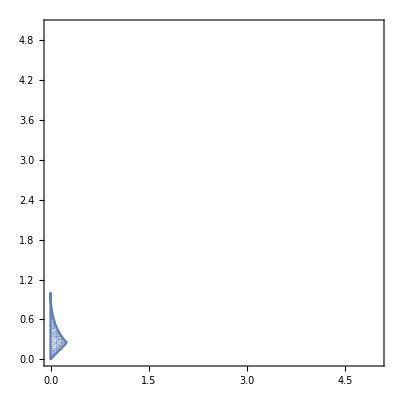

```mathematica
p2=RegionPlot[{KdFROC2[1/x2,x1/x2]},{x1,0,5},{x2,0,5},PlotPoints->60](*using the F4*)
```

Explicit series representation

```mathematica
Indac1a[y1,y2]
```

-((-1/y1)^n (1/y1)^(1-2 ϵ) y2^-ϵ (-y2/y1)^m Gamma[1-2 ϵ] Gamma[1+ϵ]^2 Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n])/(ϵ^3 m! n! Pochhammer[1-ϵ,m] Pochhammer[1-ϵ,n])+((-1/y1)^n (-y2/y1)^m Gamma[1-ϵ] Gamma[1+ϵ] Pochhammer[1,m+n] Pochhammer[1+ϵ,m+n])/(y1 ϵ^3 m! n! Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n])-1/ϵ^2 y1^ϵ y2^-ϵ ((((-1/y1)^n (1/y1)^(1-ϵ) (-y2/y1)^m Gamma[ϵ] Gamma[1+ϵ] Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n])/(m! n! Gamma[2 ϵ] Pochhammer[1-ϵ,m] Pochhammer[1-ϵ,n])+((-1/y1)^n (-y2/y1)^m Gamma[-ϵ] Gamma[1+ϵ] Pochhammer[1,m+n] Pochhammer[1-ϵ,m+n])/(y1 m! n! Gamma[1-ϵ] Gamma[ϵ] Pochhammer[1-ϵ,m] Pochhammer[1+ϵ,n])) (Log[y1]+PolyGamma[0,1-ϵ]-PolyGamma[0,-ϵ])+1/(y1 Gamma[1+m] Gamma[1+n] Gamma[ϵ] Gamma[1+n+ϵ])(-y1)^-m y2^n Gamma[1+ϵ] (((-1)^n y1^(-n+ϵ) Gamma[1+m+n] Gamma[1+m+n-ϵ] (Gamma[1-ϵ]+2 ϵ Gamma[-ϵ]) Gamma[ϵ]^2)/Gamma[1+m-ϵ]-(π Csc[π ϵ] Gamma[1+m]^2 Gamma[1+m+ϵ] (PolyGamma[0,1+m]-PolyGamma[0,1+m-n]+PolyGamma[0,ϵ]-PolyGamma[0,1+ϵ]-PolyGamma[0,1+m-n+ϵ]+PolyGamma[0,1+n+ϵ]))/(Gamma[1+m-n] Gamma[1-ϵ] Gamma[1+m-n+ϵ])))+1/ϵ^2 y1^ϵ (((-1/y1)^n (-y2/y1)^m Pochhammer[1,m+n] Pochhammer[1-ϵ,m+n] (Log[y1]-PolyGamma[0,-ϵ]+PolyGamma[0,1+ϵ]))/(y1 m! n! Pochhammer[1-ϵ,n] Pochhammer[1+ϵ,m])+(π (-y1)^-m y2^n Csc[π ϵ] (((-1)^n y1^(-n-ϵ) Gamma[1+m+n] Gamma[1+ϵ] Gamma[1+m+n+ϵ])/Gamma[1+m+ϵ]+(Gamma[1+m]^2 Gamma[1+m-ϵ] (-1+ϵ PolyGamma[0,1+m]-ϵ PolyGamma[0,1+m-n]-ϵ PolyGamma[0,1+m-n-ϵ]+ϵ PolyGamma[0,-ϵ]-ϵ PolyGamma[0,ϵ]+ϵ PolyGamma[0,1+n+ϵ]))/(ϵ Gamma[1+m-n] Gamma[1+m-n-ϵ] Gamma[-ϵ])))/(y1 Gamma[1+m] Gamma[1+n] Gamma[1+n+ϵ]))

### Ac-1b

using the above list of ACs we see that they following overlaps

```mathematica
RegionPlot[{KdFROC3[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the KdF*)
```

-Graphics-

```mathematica
RegionPlot[{F4roc6[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

```mathematica
Indac1b[y1_,y2_]:= -1/ϵ^3 y2^-ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 F4AC6[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1,y2,m,n] + 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ]F4AC6[1,1-ϵ,1-ϵ,1+ϵ,-y1,y2,m,n] -1/ϵ^2 y1^ϵ y2^-ϵ((Log[y1]+PolyGamma[1-ϵ]-PolyGamma[-ϵ])F4AC6[1,1-ϵ,1+ϵ,1-ϵ,-y1,y2,m,n]+ Limit[D[KdFAC3[1+δ,1+δ-ϵ,1,1+δ,1-ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0]) + 1/ϵ^2 y1^ϵ((Log[y1]+PolyGamma[1+ϵ]-PolyGamma[-ϵ])F4AC6[1,1+ϵ,1+ϵ,1+ϵ,-y1,y2,m,n]+ Limit[D[KdFAC3[1+δ,1+δ+ϵ,1,1+δ,1+ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0])
```

y1= 1/x2   y2= x1/x2

Region of the AC is given by that of KdF

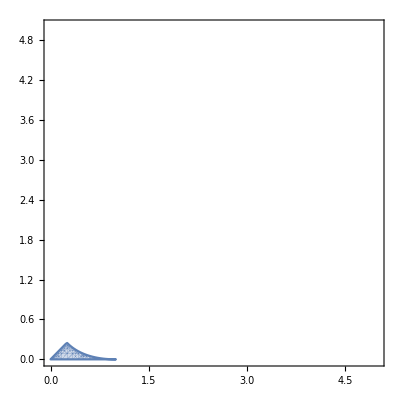

```mathematica
p3=RegionPlot[{KdFROC3[1/x2,x1/x2]},{x1,0,5},{x2,0,5},PlotPoints->60](*using the F4*)
```

```mathematica
Indac1b[y1,y2]
```

-((-1/y1)^n (1/y1)^(1-2 ϵ) y2^-ϵ (-y2/y1)^m Gamma[1-2 ϵ] Gamma[1+ϵ]^2 Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n])/(ϵ^3 m! n! Pochhammer[1-ϵ,m] Pochhammer[1-ϵ,n])+((-1/y1)^n (-y2/y1)^m Gamma[1-ϵ] Gamma[1+ϵ] Pochhammer[1,m+n] Pochhammer[1+ϵ,m+n])/(y1 ϵ^3 m! n! Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n])-1/ϵ^2 y1^ϵ y2^-ϵ (((-y1)^-m y2^-n Gamma[1+ϵ] (((-1)^n y1^(-n+ϵ) y2^(2 n) ϵ Gamma[1+m+n] Gamma[1+m+n-ϵ] Gamma[-ϵ] Gamma[ϵ]^2)/Gamma[1+m-ϵ]+((-1)^(1+m) (-y2)^m Gamma[1+m]^2 Gamma[-m+n-ϵ] Gamma[1+m+ϵ] (Gamma[-m+n] Gamma[1+n-ϵ]-2 (-y2)^ϵ Cos[π ϵ] Gamma[-m+n-2 ϵ] Gamma[1+n+ϵ]))/(Gamma[1-ϵ] Gamma[1+n-ϵ])))/(y1 Gamma[1+m] Gamma[1+n] Gamma[ϵ] Gamma[1+n+ϵ])+(((-1/y1)^n (1/y1)^(1-ϵ) (-y2/y1)^m Gamma[ϵ] Gamma[1+ϵ] Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n])/(m! n! Gamma[2 ϵ] Pochhammer[1-ϵ,m] Pochhammer[1-ϵ,n])+((-1/y1)^n (-y2/y1)^m Gamma[-ϵ] Gamma[1+ϵ] Pochhammer[1,m+n] Pochhammer[1-ϵ,m+n])/(y1 m! n! Gamma[1-ϵ] Gamma[ϵ] Pochhammer[1-ϵ,m] Pochhammer[1+ϵ,n])) (Log[y1]+PolyGamma[0,1-ϵ]-PolyGamma[0,-ϵ]))+1/ϵ^2 y1^ϵ (((-y1)^-m y2^-n (((-1)^n π y1^(-n-ϵ) y2^(2 n) Csc[π ϵ] Gamma[1+m+n] Gamma[1+ϵ] Gamma[1+m+n+ϵ])/Gamma[1+m+ϵ]+((-1)^(1+m) (-y2)^(m-ϵ) ϵ Gamma[1+m]^2 Gamma[1+m-ϵ] ((-y2)^ϵ Gamma[-m+n] Gamma[-m+n-ϵ] Gamma[1+n+ϵ]+π Csc[π ϵ] Gamma[1+n-ϵ] Gamma[-m+n+ϵ] Pochhammer[0,-m+n]))/(Gamma[1-ϵ] Gamma[1+n-ϵ])))/(y1 Gamma[1+m] Gamma[1+n] Gamma[1+n+ϵ])+((-1/y1)^n (-y2/y1)^m Pochhammer[1,m+n] Pochhammer[1-ϵ,m+n] (Log[y1]-PolyGamma[0,-ϵ]+PolyGamma[0,1+ϵ]))/(y1 m! n! Pochhammer[1-ϵ,n] Pochhammer[1+ϵ,m]))

### Ac-2

using the above list of ACs we see that they following overlaps

```mathematica
RegionPlot[{KdFROC5[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the KdF*)
```

-Graphics-

```mathematica
RegionPlot[{F4roc7[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

```mathematica
Indac2[y1_,y2_]:= -1/ϵ^3 y2^-ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 F4AC7[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1,y2,m,n] + 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ]F4AC7[1,1-ϵ,1-ϵ,1+ϵ,-y1,y2,m,n] -1/ϵ^2 y1^ϵ y2^-ϵ((Log[y1]+PolyGamma[1-ϵ]-PolyGamma[-ϵ])F4AC7[1,1-ϵ,1+ϵ,1-ϵ,-y1,y2,m,n]+ (D[KdFAC5[1+δ,1+δ-ϵ,1,1+δ,1-ϵ,1+ϵ+δ,-y1,y2,m,n],δ]/.δ-> 0)) + 1/ϵ^2 y1^ϵ((Log[y1]+PolyGamma[1+ϵ]-PolyGamma[-ϵ])F4AC7[1,1+ϵ,1+ϵ,1+ϵ,-y1,y2,m,n]+ (D[KdFAC5[1+δ,1+δ+ϵ,1,1+δ,1+ϵ,1+ϵ+δ,-y1,y2,m,n],δ]/.δ-> 0))
```

y1= 1/x2   y2= x1/x2

```mathematica
p4=RegionPlot[{KdFROC5[1/x2,x1/x2]},{x1,0,5},{x2,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

```mathematica
Indac2[y1,y2]//Simplify
```

((-1)^(1+m) (-y1)^m (-y2)^-m y2^(-1-n-ϵ) ((-y2^2)^ϵ Gamma[1-ϵ]^2 Gamma[ϵ]^2 Gamma[1+ϵ]^2 Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n]+y1^ϵ ϵ Gamma[-ϵ] Gamma[2 ϵ] Gamma[1+ϵ] Pochhammer[1,m+n] Pochhammer[1-ϵ,n] Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,m] (Log[-y2]+PolyGamma[0,1+m]-PolyGamma[0,1+m+n]+PolyGamma[0,1-ϵ]-PolyGamma[0,1+ϵ])+Gamma[1-ϵ] (y2^ϵ Gamma[-ϵ] Gamma[2 ϵ] Gamma[1+ϵ]^2 Pochhammer[1,m+n] Pochhammer[1-ϵ,n] Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,m]+Gamma[ϵ] (y1^ϵ (-y2)^ϵ ϵ Gamma[ϵ] Gamma[1+ϵ] Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n] (Log[-y2]+PolyGamma[0,1+m]+PolyGamma[0,1-ϵ]-PolyGamma[0,1+m+n-ϵ]-PolyGamma[0,1+ϵ])+Gamma[2 ϵ] (-(-y2)^(2 ϵ) Gamma[1-2 ϵ] Gamma[1+ϵ]^2 Pochhammer[1-2 ϵ,m+n] Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n]+y1^ϵ ϵ Pochhammer[1,m+n] Pochhammer[1-ϵ,m] (-Pochhammer[1-ϵ,n] Pochhammer[1+ϵ,m+n] (Log[y1]+PolyGamma[0,1-ϵ]-PolyGamma[0,-ϵ])+y2^ϵ Pochhammer[1-ϵ,m+n] Pochhammer[1+ϵ,n] (Log[y1]-Log[-y2]-PolyGamma[0,1+m]+PolyGamma[0,1+m+n]-PolyGamma[0,-ϵ]+PolyGamma[0,1+ϵ])))))))/(ϵ^3 m! n! Gamma[1-ϵ] Gamma[ϵ] Gamma[2 ϵ] Pochhammer[1-ϵ,m] Pochhammer[1-ϵ,n] Pochhammer[1+ϵ,m] Pochhammer[1+ϵ,n])

### Till this point we verify that there are indeed 4 regions instead of 3 as given in paper. From here onwards we show one extra that will help us get into the Whitezone

### Ac-3

using the above list of ACs we see that they following overlaps

```mathematica
RegionPlot[{KdFROC6[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the KdF*)
```

-Graphics-

```mathematica
RegionPlot[{F4roc5[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

```mathematica
Indac3[y1_,y2_]:= -1/ϵ^3 y2^-ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 F4AC5[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1,y2,m,n] + 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ]F4AC5[1,1-ϵ,1-ϵ,1+ϵ,-y1,y2,m,n] -1/ϵ^2 y1^ϵ y2^-ϵ((Log[y1]+PolyGamma[1-ϵ]-PolyGamma[-ϵ])F4AC5[1,1-ϵ,1+ϵ,1-ϵ,-y1,y2,m,n]+ Limit[D[KdFAC6[1+δ,1+δ-ϵ,1,1+δ,1-ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0]) + 1/ϵ^2 y1^ϵ((Log[y1]+PolyGamma[1+ϵ]-PolyGamma[-ϵ])F4AC5[1,1+ϵ,1+ϵ,1+ϵ,-y1,y2,m,n]+ Limit[D[KdFFAC6[1+δ,1+δ+ϵ,1,1+δ,1+ϵ,1+ϵ+δ,-y1,y2,m,n],δ],δ-> 0])
```

y1= 1/x2   y2= x1/x2

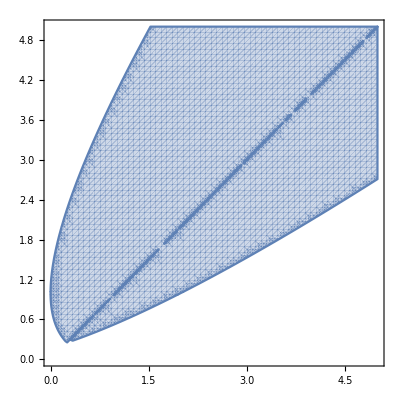

```mathematica
p5=RegionPlot[{KdFROC6[1/x2,x1/x2]},{x1,0,5},{x2,0,5},PlotPoints->60](*using the F4*)
```

### Ac-4(Here we have used the results from Appendix-E)

```mathematica
Indappe[y1_,y2_]:= 1/ϵ^3(-1)^(2ϵ)Gamma[1-2ϵ] Gamma[1+ϵ]^2 y2^(ϵ-1)f4num[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1/y2,1/y2]+ (-2/ϵ^3(-1)^ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 Cos[π ϵ] y2^(ϵ-1)f4num[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1/y2,1/y2]+ 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ] y2^-1 f4num[1,1-ϵ,1-ϵ,1+ϵ,-y1/y2,1/y2])+(t2/t1(1/ϵ^2 y1^ϵ y2^-ϵ(Log[y1]-Log[y2]-I π)f4num[1,1+ϵ,1+ϵ,1+ϵ,-y1/y2,1/y2]-1/ϵ^3 y1^ϵ(-1)^ϵ Gamma[1+ϵ]Gamma[1-ϵ]f4num[1,1-ϵ,1+ϵ,1-ϵ,-y1/y2,1/y2]+1/ϵ^2 y1^ϵ y2^-ϵ (D[KdF[{{1+δ,1+δ+ϵ},{1},{}},{{},{1+δ,1+ϵ},{1+ϵ+δ}},{-y1/y2,1/y2}],δ]/.δ-> 0)))+ (t2/t1(1/ϵ^2 y1^ϵ(Log[y2/y1]-PolyGamma[-ϵ]-PolyGamma[ϵ]-I π)f4num[1,1-ϵ,1+ϵ,1-ϵ,-y1/y2,1/y2]-1/ϵ^3 y1^ϵ(-1)^ϵ(y2)^-ϵ Gamma[1+ϵ]Gamma[1-ϵ]f4num[1,1+ϵ,1+ϵ,1+ϵ,-y1/y2,1/y2]-1/ϵ^2 y1^ϵ(D[KdF[{{1+δ,1+δ-ϵ},{1},{}},{{},{1+δ,1-ϵ},{1+ϵ+δ}},{-y1/y2,1/y2}],δ]/.δ-> 0)))
```

```mathematica
RegionPlot[{KdFROC6[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the KdF*)
```

-Graphics-

```mathematica
RegionPlot[{F4roc5[x,y]},{x,0,5},{y,0,5},PlotPoints->60](*using the F4*)
```

-Graphics-

Applying KFdFAC6 and F4AC5 in the above equation will give the following ROC

```mathematica
Indac4[y1_,y2_]:= 1/ϵ^3(-1)^(2ϵ)Gamma[1-2ϵ] Gamma[1+ϵ]^2 y2^(ϵ-1)F4AC5[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1/y2,1/y2,m,n]+ (-2/ϵ^3(-1)^ϵ Gamma[1-2ϵ] Gamma[1+ϵ]^2 Cos[π ϵ] y2^(ϵ-1)F4AC5[1-2ϵ,1-ϵ,1-ϵ,1-ϵ,-y1/y2,1/y2,m,n]+ 1/ϵ^3 Gamma[1+ϵ]Gamma[1-ϵ] y2^-1 F4AC5[1,1-ϵ,1-ϵ,1+ϵ,-y1/y2,1/y2,m,n])+(t2/t1(1/ϵ^2 y1^ϵ y2^-ϵ(Log[y1]-Log[y2]-I π)F4AC5[1,1+ϵ,1+ϵ,1+ϵ,-y1/y2,1/y2,m,n]-1/ϵ^3 y1^ϵ(-1)^ϵ Gamma[1+ϵ]Gamma[1-ϵ]F4AC5[1,1-ϵ,1+ϵ,1-ϵ,-y1/y2,1/y2,m,n]+1/ϵ^2 y1^ϵ y2^-ϵ (D[KdFAC6[{{1+δ,1+δ+ϵ},{1},{}},{{},{1+δ,1+ϵ},{1+ϵ+δ}},{-y1/y2,1/y2}],δ]/.δ-> 0)))+ (t2/t1(1/ϵ^2 y1^ϵ(Log[y2/y1]-PolyGamma[-ϵ]-PolyGamma[ϵ]-I π)F4AC5[1,1-ϵ,1+ϵ,1-ϵ,-y1/y2,1/y2]-1/ϵ^3 y1^ϵ(-1)^ϵ(y2)^-ϵ Gamma[1+ϵ]Gamma[1-ϵ]F4AC5[1,1+ϵ,1+ϵ,1+ϵ,-y1/y2,1/y2]-1/ϵ^2 y1^ϵ(D[KdFAC6[{{1+δ,1+δ-ϵ},{1},{}},{{},{1+δ,1-ϵ},{1+ϵ+δ}},{-y1/y2,1/y2}],δ]/.δ-> 0)))
```

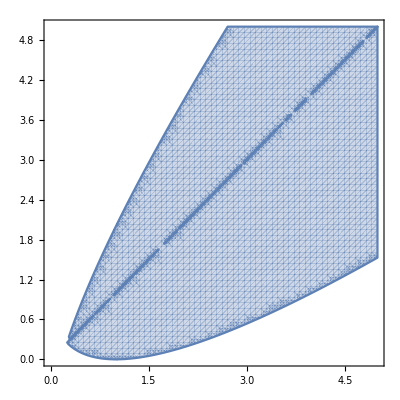

```mathematica
p6=RegionPlot[{KdFROC6[(-1/x2)/(x1/x2),1/(x1/x2)]},{x1,0,5},{x2,0,5},PlotPoints->60]
```

## All plots together

The 4- regions

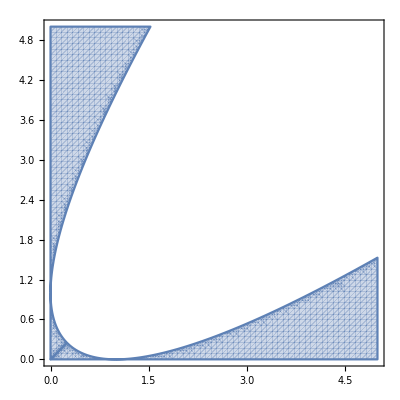

```mathematica
Show[p1,p2,p3,p4]
```

All the ACs along with the newly found AC3 and AC-4 plotted together

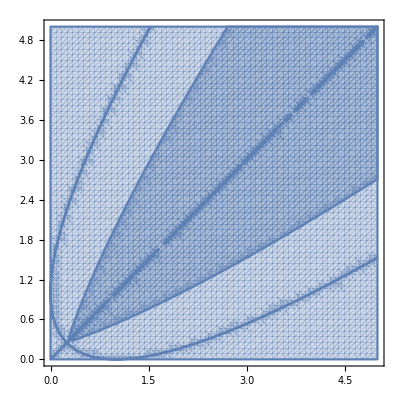

```mathematica
Show[p1,p2,p3,p4,p5,p6]
```